# Spatially Adaptive Finite Volume Method For Moment Models

This Mathematica file implements a spatially adaptive finite volume method for moment models. The spatial adaptivity allows the simulation to use a different number of moments (and so different models) in different parts of the domain. Currently, the setting is the following: the domain is divided in 2 subdomains. In the left subdomain, the number of moments (=: ML) is smaller than the number of moments (=: MR) in the right subdomain. 
In this code, the interface between the two models is at the shock.

## Construction of Spatially Adaptive Moment Model

Construction of the spatial discretization matrix of the models. The construction is split into transport part (Roe matrix and viscosity matrix) and source term part (relaxation).

### Source Term

Computation of source term.

#### Extended vector models

Construction of the source term matrix for the models using the extended vector.

```mathematica
ConstructSourceTerm[nxL_,nxR_,x1_,x2_,momentsLeft_,momentsRight_,Relaxation_,dt_]:=Block[{SourceMatrixLeft,SourceMatrixRight,SourceTermVectorLeft,SourceTermVectorRight,SourceTermVector},
(* For the RHS source term, we assume a BGK-type operator and we assume that the source term matrix is a diagonal matrix *)
SourceMatrixLeft =SparseArray[{{i_,i_}/;i>=4:>1},{momentsLeft,momentsLeft}];
SourceMatrixRight =SparseArray[{{i_,i_}/;i>=4:>1},{momentsRight,momentsRight}];

SourceMatrix =ConstantArray[0,{n+2,n+2}];

For[i=2,i<=nxL,i++,
For[j=1,j<i,j++,
SourceMatrix[[i,j]]=ConstantArray[0,{momentsLeft,momentsLeft}]
];
SourceMatrix[[i,i]]=SourceMatrixLeft;
For[j=i+1,j<=nxL,j++,
SourceMatrix[[i,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
];
For[j=nxL+1,j<=n+2,j++,
SourceMatrix[[i,j]]=ConstantArray[0,{momentsLeft,momentsRight}];
];
];

For[i=nxL+1,i<=n+1,i++,
For[j=1,j<=nxL,j++,
SourceMatrix[[i,j]]=ConstantArray[0,{momentsRight,momentsLeft}]
];
For[j=nxL+1,j<i,j++,
SourceMatrix[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];
SourceMatrix[[i,i]]=SourceMatrixRight;
For[j=i+1,j++,j<=n+2,
SourceMatrix[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];
];

SourceMatrix[[1,1]]=ConstantArray[0,{momentsLeft,momentsLeft}];
SourceMatrix[[n+2,n+2]]=ConstantArray[0,{momentsRight,momentsRight}];

SourceTermVectorLeft={0,0,0};
SourceTermVectorRight={0,0,0};

For[i=4,i<=momentsLeft,i++,
SourceTermVectorLeft=Append[SourceTermVectorLeft,1];
SourceTermVectorRight=Append[SourceTermVectorRight,1];
];
For[i=momentsLeft+1,i<=momentsRight,i++,
SourceTermVectorRight=Append[SourceTermVectorRight,1];
];
SourceTermVector={};
For[i=0,i<nxL,i++,
SourceTermVector=Join[SourceTermVector,SourceTermVectorLeft];
];
For[i=nxL,i<=n+1,i++,
SourceTermVector=Join[SourceTermVector,SourceTermVectorRight];
];
(* Obtain source term vector *)
SourceTermVector=-1/Relaxation*SourceTermVector;
SourceMatrix=1/Relaxation*SourceMatrix;

(* Obtain Exponential of source term vector *)
SourceTermVector=Exp[SourceTermVector*dt];

SourceTermMatrix=DiagonalMatrix[SourceTermVector];
];
```

#### Non-square matrix models

Construction of the source term for the model that used non-square matrices.

```mathematica
ConstructSourceTermNonSquare[nxL_,nxR_,x1_,x2_,momentsLeft_,momentsRight_,Relaxation_,dt_]:=Block[{SourceMatrixLeft,SourceMatrixRight,SourceTermVectorLeft,SourceTermVectorRight,SourceTermVector},
(* For the RHS source term, we assume a BGK-type operator and we assume that the source term matrix is a diagonal matrix *)
SourceMatrixLeft =SparseArray[{{i_,i_}/;i>=4:>1},{momentsLeft,momentsLeft}];
SourceMatrixRight =SparseArray[{{i_,i_}/;i>=4:>1},{momentsRight,momentsRight}];

SourceMatrixNonSquare =ConstantArray[0,{n+2,n+2}];

For[i=2,i<=nxL+1,i++,
For[j=1,j<i,j++,
SourceMatrixNonSquare[[i,j]]=ConstantArray[0,{momentsLeft,momentsLeft}]
];
SourceMatrixNonSquare[[i,i]]=SourceMatrixLeft;
For[j=i+1,j<=nxL+1,j++,
SourceMatrixNonSquare[[i,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
];
For[j=nxL+2,j<=n+2,j++,
SourceMatrixNonSquare[[i,j]]=ConstantArray[0,{momentsLeft,momentsRight}];
];
];

For[i=nxL+2,i<=n+1,i++,
For[j=1,j<=nxL+1,j++,
SourceMatrixNonSquare[[i,j]]=ConstantArray[0,{momentsRight,momentsLeft}]
];
For[j=nxL+2,j<i,j++,
SourceMatrixNonSquare[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];
SourceMatrixNonSquare[[i,i]]=SourceMatrixRight;
For[j=i+1,j++,j<=n+2,
SourceMatrixNonSquare[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];
];

SourceMatrixNonSquare[[1,1]]=ConstantArray[0,{momentsLeft,momentsLeft}];
SourceMatrixNonSquare[[n+2,n+2]]=ConstantArray[0,{momentsRight,momentsRight}];

SourceTermVectorLeft={0,0,0};
SourceTermVectorRight={0,0,0};

For[i=4,i<=momentsLeft,i++,
SourceTermVectorLeft=Append[SourceTermVectorLeft,1];
SourceTermVectorRight=Append[SourceTermVectorRight,1];
];
For[i=momentsLeft+1,i<=momentsRight,i++,
SourceTermVectorRight=Append[SourceTermVectorRight,1];
];
SourceTermVector={};
For[i=0,i<nxL+1,i++,
SourceTermVector=Join[SourceTermVector,SourceTermVectorLeft];
];
For[i=nxL+1,i<=n+1,i++,
SourceTermVector=Join[SourceTermVector,SourceTermVectorRight];
];
(* Obtain source term vector *)
SourceTermVector=-1/Relaxation*SourceTermVector;
SourceMatrixNonSquare=1/Relaxation*SourceMatrixNonSquare;

(* Obtain Exponential of source term vector *)
SourceTermVector=Exp[SourceTermVector*dt];

SourceTermMatrixNonSquare=DiagonalMatrix[SourceTermVector];
];
```

### Construction of model at the interface between the two subdomains

There are different options for the model we use in the cell directly right of the interface between the left and the right subdomains, in which a different number of moments is used.

#### Using the extended vector by padding the smaller vector with a zero

```mathematica
(* Here we use the zero-padded extended vector model in the cells at the interface and apply a correction for not having a non-zero value for the last moment in the cell left of the interface *)
zeroPaddedModelAtInterface[]:=Block[{},
ARightLastColumns=ARight;
QRightLastColumns=QRight;
ARightLastRowsWithoutLastColumns=ARight;
QRightLastRowsWithoutLastColumns=QRight;
ARightLastColumns[[All,1;;momentsLeft]]=0;
QRightLastColumns[[All,1;;momentsLeft]]=0;
ARightLastRowsWithoutLastColumns[[1;;momentsLeft,All]]=0;
QRightLastRowsWithoutLastColumns[[1;;momentsLeft,All]]=0;
ARightLastRowsWithoutLastColumns[[All,momentsLeft+1;;momentsRight]]=0;
QRightLastRowsWithoutLastColumns[[All,momentsLeft+1;;momentsRight]]=0;

RoeZeroPaddedModel[[nxL+2,nxL+1]]=-ATilde;
RoeZeroPaddedModel[[nxL+2,nxL+1]][[All,-numberOfMomentsDifference;;-1]]=0;
RoeZeroPaddedModel[[nxL+2,nxL+2]]=-ARightLastColumns-ARightLastRowsWithoutLastColumns;
(*RoeZeroPaddedModel[[nxL+2,nxL+2]]=-ARightLastRowsWithoutLastColumns;*) (* This gives the uncorrected method *)
RoeZeroPaddedModel[[nxL+2,nxL+3]]=ARight;
ViscosityZeroPaddedModel[[nxL+2,nxL+1]]=-QTilde;
ViscosityZeroPaddedModel[[nxL+2,nxL+1]][[All,-numberOfMomentsDifference;;-1]]=0;
ViscosityZeroPaddedModel[[nxL+2,nxL+2]]=2*QRight-QRightLastColumns-QRightLastRowsWithoutLastColumns;
(*ViscosityZeroPaddedModel[[nxL+2,nxL+2]]=2*QRight-QRightLastRowsWithoutLastColumns;*) (* This gives the uncorrected method *)
ViscosityZeroPaddedModel[[nxL+2,nxL+3]]=-QRight;
];
```

#### Using the extended vector by padding the smaller vector with the last moment(s) of the neighbouring bigger vector

```mathematica
(* Here we use the non-zero extended vector model for the extended vector in the cells at the interface *)
nonZeroPaddedModelAtInterface[]:=Block[{},
ARightLastColumns=ARight;
QRightLastColumns=QRight;
ARightLastColumns[[All,1;;momentsLeft]]=0;
QRightLastColumns[[All,1;;momentsLeft]]=0;

RoeNonZeroPaddedModel[[nxL+2,nxL+1]]=-ARight;
RoeNonZeroPaddedModel[[nxL+2,nxL+1]][[All,-numberOfMomentsDifference;;-1]]=0;
RoeNonZeroPaddedModel[[nxL+2,nxL+2]]=-ARightLastColumns;
RoeNonZeroPaddedModel[[nxL+2,nxL+3]]=ARight;
ViscosityNonZeroPaddedModel[[nxL+2,nxL+1]]=-QRight;
ViscosityNonZeroPaddedModel[[nxL+2,nxL+1]][[All,-numberOfMomentsDifference;;-1]]=0;
ViscosityNonZeroPaddedModel[[nxL+2,nxL+2]]=2*QRight-QRightLastColumns;
ViscosityNonZeroPaddedModel[[nxL+2,nxL+3]]=-QRight;
];
```

#### Using non-square matrices

```mathematica
NonSquareMatricesAtInterface[]:=(

For[j=1,j<=nxL+1,j++,
RoeNonSquareMatrices[[1,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
ViscosityNonSquareMatrices[[1,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
];

For[j=nxL+2,j<=n+2,j++,
RoeNonSquareMatrices[[1,j]]=ConstantArray[0,{momentsLeft,momentsRight}];
ViscosityNonSquareMatrices[[1,j]]=ConstantArray[0,{momentsLeft,momentsRight}];
];

(* Rows corresponding to moment model of order ML *)
For[i=2,i<=nxL,i++,
RoeNonSquareMatrices[[i,i-1]]=-ALeft;
RoeNonSquareMatrices[[i,i]]=ConstantArray[0,{momentsLeft,momentsLeft}];
RoeNonSquareMatrices[[i,i+1]]=ALeft;
ViscosityNonSquareMatrices[[i,i-1]]=-QLeft;
ViscosityNonSquareMatrices[[i,i]]=2*QLeft;
ViscosityNonSquareMatrices[[i,i+1]]=-QLeft;

For[j=1,j<i-1,j++,
RoeNonSquareMatrices[[i,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
ViscosityNonSquareMatrices[[i,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
];

For[j=i+2,j<=nxL+1,j++,
RoeNonSquareMatrices[[i,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
ViscosityNonSquareMatrices[[i,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
];

For[j=nxL+2,j<=n+2,j++,
RoeNonSquareMatrices[[i,j]]=ConstantArray[0,{momentsLeft,momentsRight}];
ViscosityNonSquareMatrices[[i,j]]=ConstantArray[0,{momentsLeft,momentsRight}];
];
];

RoeNonSquareMatrices[[nxL+1,nxL]]=-ALeft;
RoeNonSquareMatrices[[nxL+1,nxL+1]]=ConstantArray[0,{momentsLeft,momentsLeft}];
RoeNonSquareMatrices[[nxL+1,nxL+2]]=ARight[[;;-(numberOfMomentsDifference+1),;;]];
ViscosityNonSquareMatrices[[nxL+1,nxL]]=-QLeft;
ViscosityNonSquareMatrices[[nxL+1,nxL+1]]=2*QLeft;
ViscosityNonSquareMatrices[[nxL+1,nxL+2]]=-QRight[[;;-(numberOfMomentsDifference+1),;;]];
For[j=1,j<nxL,j++,
RoeNonSquareMatrices[[nxL+1,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
ViscosityNonSquareMatrices[[nxL+1,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
];
For[j=nxL+3,j<=n+2,j++,
RoeNonSquareMatrices[[nxL+1,j]]=ConstantArray[0,{momentsLeft,momentsRight}];
ViscosityNonSquareMatrices[[nxL+1,j]]=ConstantArray[0,{momentsLeft,momentsRight}];
];

RoeNonSquareMatrices[[nxL+2,nxL+1]]=-ARight[[;;,;;-(numberOfMomentsDifference+1)]];
RoeNonSquareMatrices[[nxL+2,nxL+2]]=ConstantArray[0,{momentsRight,momentsRight}];
RoeNonSquareMatrices[[nxL+2,nxL+3]]=ARight;
ViscosityNonSquareMatrices[[nxL+2,nxL+1]]=-QRight[[;;,;;-(numberOfMomentsDifference+1)]];
ViscosityNonSquareMatrices[[nxL+2,nxL+2]]=2*QRight;
ViscosityNonSquareMatrices[[nxL+2,nxL+3]]=-QRight;

For[i=nxL+3,i<n+2,i++,
RoeNonSquareMatrices[[i,i-1]]=-ARight;
RoeNonSquareMatrices[[i,i]]=ConstantArray[0,{momentsRight,momentsRight}];
RoeNonSquareMatrices[[i,i+1]]=ARight;

ViscosityNonSquareMatrices[[i,i-1]]=-QRight;
ViscosityNonSquareMatrices[[i,i]]=2*QRight;
ViscosityNonSquareMatrices[[i,i+1]]=-QRight;

For[j=1,j<=nxL+1,j++,
RoeNonSquareMatrices[[i,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
ViscosityNonSquareMatrices[[i,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
];

For[j=nxL+2,j<i-1,j++,
RoeNonSquareMatrices[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
ViscosityNonSquareMatrices[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];

For[j=i+2,j<=n+2,j++,
RoeNonSquareMatrices[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
ViscosityNonSquareMatrices[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];
];

For[j=1,j<=nxL+1,j++,
RoeNonSquareMatrices[[n+2,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
ViscosityNonSquareMatrices[[n+2,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
];

For[j=nxL+2,j<=n+2,j++,
RoeNonSquareMatrices[[n+2,j]]=ConstantArray[0,{momentsRight,momentsRight}];
ViscosityNonSquareMatrices[[n+2,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];
)
```

### Construction matrix

Construction of the Roe matrix and the viscosity matrix.

```mathematica
ConstructMatrix[nxL_,nxR_,x1_,x2_,dx_,momentsLeft_,momentsRight_,Relaxation_,dt_]:=Block[{},

(* Define the model matrices *)
ALeft=SparseArray[{{i_,j_}/;i-j==1:>Sqrt[j],{i_,j_}/;j-i==1:>Sqrt[i]},{momentsLeft,momentsLeft}];
ARight=SparseArray[{{i_,j_}/;i-j==1:>Sqrt[j],{i_,j_}/;j-i==1:>Sqrt[i]},{momentsRight,momentsRight}];
ATilde=ARight;
ATilde[[-numberOfMomentsDifference;;-1,All]]=0;

(* Define the numerical viscosity matrices *)
QLeft=IdentityMatrix[momentsLeft];
QRight=IdentityMatrix[momentsRight];
QTilde=QRight;
QTilde[[-numberOfMomentsDifference;;-1,All]]=0;

(* Initialize block matrices for the different models *)
RoeZeroPaddedModel = ConstantArray[0,{n+2,n+2}];
ViscosityZeroPaddedModel=ConstantArray[0,{n+2,n+2}];

RoeNonZeroPaddedModel = ConstantArray[0,{n+2,n+2}];
ViscosityNonZeroPaddedModel=ConstantArray[0,{n+2,n+2}];

RoeNonSquareMatrices = ConstantArray[0,{n+2,n+2}];
ViscosityNonSquareMatrices=ConstantArray[0,{n+2,n+2}];

(* CREATE THE SPATIAL DISCRETIZATION MATRIX BLOCK BY BLOCK *)

(* First row is a ghost row *)
For[j=1,j<=nxL,j++,
RoeZeroPaddedModel[[1,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
ViscosityZeroPaddedModel[[1,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
];

For[j=nxL+1,j<=n+2,j++,
RoeZeroPaddedModel[[1,j]]=ConstantArray[0,{momentsLeft,momentsRight}];
ViscosityZeroPaddedModel[[1,j]]=ConstantArray[0,{momentsLeft,momentsRight}];
];

(* Rows corresponding to moment model of order ML *)
For[i=2,i<nxL,i++,
RoeZeroPaddedModel[[i,i-1]]=-ALeft;
RoeZeroPaddedModel[[i,i]]=ConstantArray[0,{momentsLeft,momentsLeft}];
RoeZeroPaddedModel[[i,i+1]]=ALeft;
ViscosityZeroPaddedModel[[i,i-1]]=-QLeft;
ViscosityZeroPaddedModel[[i,i]]=2*QLeft;
ViscosityZeroPaddedModel[[i,i+1]]=-QLeft;

For[j=1,j<i-1,j++,
RoeZeroPaddedModel[[i,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
ViscosityZeroPaddedModel[[i,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
];

For[j=i+2,j<=nxL,j++,
RoeZeroPaddedModel[[i,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
ViscosityZeroPaddedModel[[i,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
];

For[j=nxL+1,j<=n+2,j++,
RoeZeroPaddedModel[[i,j]]=ConstantArray[0,{momentsLeft,momentsRight}];
ViscosityZeroPaddedModel[[i,j]]=ConstantArray[0,{momentsLeft,momentsRight}];
];
];

(* Row nxL (corresponds to vector nxL-1 because of the introduced ghost rows *) 
RoeZeroPaddedModel[[nxL,nxL-1]]=-ALeft;
RoeZeroPaddedModel[[nxL,nxL]]=ConstantArray[0,{momentsLeft,momentsLeft}];
RoeZeroPaddedModel[[nxL,nxL+1]]=ArrayPad[ALeft,{{0,0},{0,numberOfMomentsDifference}}];
ViscosityZeroPaddedModel[[nxL,nxL-1]]=-QLeft;
ViscosityZeroPaddedModel[[nxL,nxL]]=2*QLeft;
ViscosityZeroPaddedModel[[nxL,nxL+1]]=-ArrayPad[QLeft,{{0,0},{0,numberOfMomentsDifference}}];

For[j=1,j<nxL-1,j++,
RoeZeroPaddedModel[[nxL,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
ViscosityZeroPaddedModel[[nxL,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
];

For[j=nxL+2,j<=n+2,j++,
RoeZeroPaddedModel[[nxL,j]]=ConstantArray[0,{momentsLeft,momentsRight}];
ViscosityZeroPaddedModel[[nxL,j]]=ConstantArray[0,{momentsLeft,momentsRight}];
];

(* Row nxL+1 (correspond to vector nxL because of the introduced  ghost rows *)
ATildeLastColumns=ATilde;
QTildeLastColumns=QTilde;
ATildeLastColumns[[All,1;;momentsLeft]]=0;
QTildeLastColumns[[All,1;;momentsLeft]]=0;

RoeZeroPaddedModel[[nxL+1,nxL]]=-ArrayPad[ALeft,{{0,numberOfMomentsDifference},{0,0}}];
RoeZeroPaddedModel[[nxL+1,nxL+1]]=ConstantArray[0,{momentsRight,momentsRight}];
(*RoeWeightedModel[[nxL+1,nxL+2]]=ArrayPad[ALeft,{{0,numberOfMomentsDifference},{0,numberOfMomentsDifference}}];*)
RoeZeroPaddedModel[[nxL+1,nxL+2]]=ATilde-ATildeLastColumns;
ViscosityZeroPaddedModel[[nxL+1,nxL]]=-ArrayPad[QLeft,{{0,numberOfMomentsDifference},{0,0}}];
ViscosityZeroPaddedModel[[nxL+1,nxL+1]]=2*ArrayPad[QLeft,{{0,numberOfMomentsDifference},{0,numberOfMomentsDifference}}];
(*ViscosityWeightedSum[[nxL+1,nxL+2]]=-ArrayPad[QLeft,{{0,numberOfMomentsDifference},{0,numberOfMomentsDifference}}];*)
ViscosityZeroPaddedModel[[nxL+1,nxL+2]]=-QTilde+QTildeLastColumns;

For[j=1,j<nxL,j++,
RoeZeroPaddedModel[[nxL+1,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
ViscosityZeroPaddedModel[[nxL+1,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
];

For[j=nxL+3,j<=n+2,j++,
RoeZeroPaddedModel[[nxL+1,j]]=ConstantArray[0,{momentsRight,momentsRight}];
ViscosityZeroPaddedModel[[nxL+1,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];

(* Row nxL+2 (corresponds to vector nxL+1 because of the introduced ghost rows *)
RoeZeroPaddedModel[[nxL+2,nxL+1]]=-ARight;
RoeZeroPaddedModel[[nxL+2,nxL+1]][[All,-numberOfMomentsDifference;;-1]]=0;
RoeZeroPaddedModel[[nxL+2,nxL+2]]=ConstantArray[0,{momentsRight,momentsRight}];
RoeZeroPaddedModel[[nxL+2,nxL+3]]=ARight;
ViscosityZeroPaddedModel[[nxL+2,nxL+1]]=-QRight;
ViscosityZeroPaddedModel[[nxL+2,nxL+1]][[All,-numberOfMomentsDifference;;-1]]=0;
ViscosityZeroPaddedModel[[nxL+2,nxL+2]]=2*QRight;
ViscosityZeroPaddedModel[[nxL+2,nxL+3]]=-QRight;

For[j=1,j<=nxL,j++,
RoeZeroPaddedModel[[nxL+2,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
ViscosityZeroPaddedModel[[nxL+2,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
];

For[j=nxL+4,j<=n+2,j++,
RoeZeroPaddedModel[[nxL+2,j]]=ConstantArray[0,{momentsRight,momentsRight}];
ViscosityZeroPaddedModel[[nxL+2,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];

(* Rows corresponding to moment model of order MR (without the last one) *)
For[i=nxL+3,i<n+2,i++,
RoeZeroPaddedModel[[i,i-1]]=-ARight;
RoeZeroPaddedModel[[i,i]]=ConstantArray[0,{momentsRight,momentsRight}];
RoeZeroPaddedModel[[i,i+1]]=ARight;

ViscosityZeroPaddedModel[[i,i-1]]=-QRight;
ViscosityZeroPaddedModel[[i,i]]=2*QRight;
ViscosityZeroPaddedModel[[i,i+1]]=-QRight;

For[j=1,j<=nxL,j++,
RoeZeroPaddedModel[[i,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
ViscosityZeroPaddedModel[[i,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
];

For[j=nxL+1,j<i-1,j++,
RoeZeroPaddedModel[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
ViscosityZeroPaddedModel[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];

For[j=i+2,j<=n+2,j++,
RoeZeroPaddedModel[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
ViscosityZeroPaddedModel[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];
];

(* Last rows are ghost rows *)
For[j=1,j<=nxL,j++,
RoeZeroPaddedModel[[n+2,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
ViscosityZeroPaddedModel[[n+2,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
];

For[j=nxL+1,j<=n+2,j++,
RoeZeroPaddedModel[[n+2,j]]=ConstantArray[0,{momentsRight,momentsRight}];
ViscosityZeroPaddedModel[[n+2,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];

(* Call methods for using the zero-padded extended vector model, using the non-zero padded extended vector model at the interface and using the model with non-square matrices at the interface. *)
RoeNonZeroPaddedModel=RoeZeroPaddedModel;
ViscosityNonZeroPaddedModel=ViscosityZeroPaddedModel;
nonZeroPaddedModelAtInterface[];
zeroPaddedModelAtInterface[];

RoeNonSquareMatrices=RoeZeroPaddedModel;
ViscosityNonSquareMatrices=ViscosityZeroPaddedModel;
NonSquareMatricesAtInterface[];

(* Obtain full matrices from their block form *)
RoeZeroPaddedModelFlatten = ArrayFlatten[RoeZeroPaddedModel];
ViscosityZeroPaddedModelFlatten = ArrayFlatten[ViscosityZeroPaddedModel];

RoeNonZeroPaddedModelFlatten = ArrayFlatten[RoeNonZeroPaddedModel];
ViscosityNonZeroPaddedModelFlatten = ArrayFlatten[ViscosityNonZeroPaddedModel];

RoeNonSquareMatrixFlatten = ArrayFlatten[RoeNonSquareMatrices];
ViscosityNonSquareMatrixFlatten = ArrayFlatten[ViscosityNonSquareMatrices];

(* Call the method that construct the source term *)
ConstructSourceTerm[nxL,nxR,x1,x2,momentsLeft,momentsRight,Relaxation,dt];
ConstructSourceTermNonSquare[nxL,nxR,x1,x2,momentsLeft,momentsRight,Relaxation,dt];

(* Obtain transport part of spatial discretization matrix from Roe block matrix and viscosity block matrix *)

BigAMatrixZeroPaddedModel=-1.0/(2*dx)*(RoeZeroPaddedModel+ViscosityZeroPaddedModel);
BigAMatrixZeroPaddedModelFlatten = -1.0/(2*dx)*(RoeZeroPaddedModelFlatten+ViscosityZeroPaddedModelFlatten);

BigAMatrixNonZeroPaddedModel=-1.0/(2*dx)*(RoeNonZeroPaddedModel+ViscosityNonZeroPaddedModel);
BigAMatrixNonZeroPaddedModelFlatten = -1.0/(2*dx)*(RoeNonZeroPaddedModelFlatten+ViscosityNonZeroPaddedModelFlatten);
BigAMatrixNonSquareMatrix=-1.0/(2*dx)*(RoeNonSquareMatrices+ViscosityNonSquareMatrices);
BigAMatrixNonSquareMatrixFlatten = -1.0/(2*dx)*(RoeNonSquareMatrixFlatten+ViscosityNonSquareMatrixFlatten);

];
```

## Construction of Reference Solution

As reference solution, we consider the numerical solution we obtain if we used the bigger matrix in the whole domain.

### Source Term

Construction of the source term matrix for the reference system.

```mathematica
ConstructSourceTermReference[nxL_,nxR_,x1_,x2_,momentsLeft_,momentsRight_,Relaxation_,dt_]:=Block[{SourceMatrixRight,SourceTermVectorReference,SourceTermVectorRight},
(* For the RHS source term, we assume a BGK-type operator and we assume that the source term matrix is a diagonal matrix *)
SourceMatrixReference =ConstantArray[0,{n+2,n+2}];

SourceMatrixRight =SparseArray[{{i_,i_}/;i>=4:>1},{momentsRight,momentsRight}];

For[i=2,i<=n+1,i++,
For[j=1,j<i,j++,
SourceMatrixReference[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}]
];
SourceMatrixReference[[i,i]]=SourceMatrixRight;
For[j=i+1,j<=n+2,j++,
SourceMatrixReference[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];
];

SourceMatrixReference[[1,1]]=ConstantArray[0,{momentsRight,momentsRight}];
SourceMatrixReference[[n+2,n+2]]=ConstantArray[0,{momentsRight,momentsRight}];

SourceTermVectorRight={0,0,0};

For[i=4,i<=momentsRight,i++,
SourceTermVectorRight=Append[SourceTermVectorRight,1];
];

SourceTermVectorReference={};
For[i=0,i<=n+1,i++,
SourceTermVectorReference=Join[SourceTermVectorReference,SourceTermVectorRight];
];

(* Obtain source term vector *)
SourceTermVectorReference=-1/Relaxation*SourceTermVectorReference;
SourceMatrixReference=1/Relaxation*SourceMatrixReference;

(* Obtain Exponential of source term vector *)
SourceTermVectorReference=Exp[SourceTermVectorReference*dt];

SourceTermMatrixReference=DiagonalMatrix[SourceTermVectorReference];
];
```

### Construction matrix

Construction of the Roe matrix and the viscosity matrix for the reference system.

```mathematica
ConstructMatrixReference[nxL_,nxR_,x1_,x2_,dx_,momentsLeft_,momentsRight_,Relaxation_,dt_]:=Block[{RoeReference,ViscosityReference},
RoeReference = ConstantArray[0,{n+2,n+2}];
ViscosityReference=ConstantArray[0,{n+2,n+2}];

(* CREATE THE SPATIAL DISCRETIZATION MATRIX BLOCK BY BLOCK *)

(* First row is a ghost row *)
For[j=1,j<=n+2,j++,
RoeReference[[1,j]]=ConstantArray[0,{momentsRight,momentsRight}];
ViscosityReference[[1,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];

(* All rows apart from the first and the last *)
For[i=2,i<=n+1,i++,
RoeReference[[i,i-1]]=-ARight;
RoeReference[[i,i]]=ConstantArray[0,{momentsRight,momentsRight}];
RoeReference[[i,i+1]]=ARight;
ViscosityReference[[i,i-1]]=-QRight;
ViscosityReference[[i,i]]=2*QRight;
ViscosityReference[[i,i+1]]=-QRight;

For[j=1,j<i-1,j++,
RoeReference[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
ViscosityReference[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];

For[j=i+2,j<=n+2,j++,
RoeReference[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
ViscosityReference[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];
];

(* Last rows are ghost rows *)
For[j=1,j<=n+2,j++,
RoeReference[[n+2,j]]=ConstantArray[0,{momentsRight,momentsRight}];
ViscosityReference[[n+2,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];

(* Call the method that constructs the source term for the reference system *)
ConstructSourceTermReference[nxL,nxR,x1,x2,momentsLeft,momentsRight,Relaxation,dt];

(* Obtain full Roe matrix and full viscosity matrix from their block form *)
RoeFlattenReference = ArrayFlatten[RoeReference];
ViscosityFlattenReference = ArrayFlatten[ViscosityReference];

(* Obtain transport part of spatial discretization matrix for the reference system from Roe block matrix and viscosity block matrix *)
BigAMatrixReference=-1.0/(2*dx)*(RoeReference+ViscosityReference);
BigAMatrixFlattenReference = -1.0/(2*dx)*(RoeFlattenReference+ViscosityFlattenReference);
];
```

## Simulation Setup

Initialize model: construct vector with initial values, set parameters and call the spatial discretization matrices constructor functions.

### Construct vector with initial values for the extended vector models

Construct vector with the chosen initial values, for the models using the extended vector.

```mathematica
InitializeVector[initialValuesLeft_,initialValuesRight_,epsilon_,momentsBig_,momentsLeft_,momentsRight_]:=
Block[{values,valuesReference,momentSmall,initialValuesLeft2,initialValuesRight2,initialValuesLeftReference,initialValuesRightReference},

momentSmall=epsilon;

(* Construct the inital value vector in every part of the domain step-by-step *)
initialValuesLeft2=initialValuesLeft;
initialValuesRight2=initialValuesRight;
initialValuesLeftReference =initialValuesLeft;
initialValuesRightReference=initialValuesRight;

For[i=4,i<=momentsLeft,i++,
initialValuesLeft2=Append[initialValuesLeft2,momentsBig];
initialValuesRight2=Append[initialValuesRight2,momentsBig];
initialValuesLeftReference=Append[initialValuesLeftReference,momentsBig];
initialValuesRightReference=Append[initialValuesRightReference,momentsBig];
];
For[i=momentsLeft+1,i<=momentsRight,i++,
initialValuesRight2=Append[initialValuesRight2,momentSmall];
initialValuesLeftReference=Append[initialValuesLeftReference,momentSmall];
initialValuesRightReference=Append[initialValuesRightReference,momentSmall];
];

(* Construct big initial vector by stacking the initial vectors in each cell *)
Wraw={};
WrawReference={};
For[i=0,i<nxL+positionInFrontOfShock,i++,
values[i]=initialValuesLeft2;
Wraw=Join[Wraw,values[i]];
valuesReference[i]=initialValuesLeftReference;
WrawReference=Join[WrawReference,valuesReference[i]];
];
values[nxL]=ArrayPad[initialValuesLeft2,{0,numberOfMomentsDifference}]; (* Take initial values from the left and add zeroes *)
Wraw=Join[Wraw,values[nxL]];
valuesReference[nxL]=initialValuesLeftReference;
WrawReference=Join[WrawReference,valuesReference[nxL]];
For[i=1+positionInFrontOfShock,i<=nxR+1,i++,
values[i+positionInFrontOfShock+nxL]=initialValuesRight2;
Wraw=Join[Wraw,values[i+positionInFrontOfShock+nxL]];
valuesReference[i+positionInFrontOfShock]=initialValuesRightReference;
WrawReference=Join[WrawReference,valuesReference[i+positionInFrontOfShock]];
];
];
```

### Construct vector with initial values for non-square matrix models

```mathematica
InitializeVectorNonSquare[initialValuesLeft_,initialValuesRight_,epsilon_,momentsBig_,momentsLeft_,momentsRight_]:=
Block[{values,valuesReference,momentSmall,initialValuesLeft2,initialValuesRight2,initialValuesLeftReference,initialValuesRightReference},

momentSmall=epsilon;

(* Construct the inital value vector in every part of the domain step-by-step *)
initialValuesLeft2=initialValuesLeft;
initialValuesRight2=initialValuesRight;
initialValuesLeftReference =initialValuesLeft;
initialValuesRightReference=initialValuesRight;

For[i=4,i<=momentsLeft,i++,
initialValuesLeft2=Append[initialValuesLeft2,momentsBig];
initialValuesRight2=Append[initialValuesRight2,momentsBig];
initialValuesLeftReference=Append[initialValuesLeftReference,momentsBig];
initialValuesRightReference=Append[initialValuesRightReference,momentsBig];
];
For[i=momentsLeft+1,i<=momentsRight,i++,
initialValuesRight2=Append[initialValuesRight2,momentSmall];
initialValuesLeftReference=Append[initialValuesLeftReference,momentSmall];
initialValuesRightReference=Append[initialValuesRightReference,momentSmall];
];

(* Construct big initial vector by stacking the initial vectors in each cell *)
Wraw={};
For[i=0,i<nxL+1,i++,
values[i]=initialValuesLeft2;
Wraw=Join[Wraw,values[i]];
];
For[i=1,i<=nxR+1,i++,
values[i+nxL]=initialValuesRight2;
Wraw=Join[Wraw,values[i+nxL]];
];
];
```

### Set up model

Set spatial discretization parameters and call the spatial discretization matrix construction functions.

```mathematica
InitializeModel[nxL_,nxR_,x1_,x2_,momentsLeft_,momentsRight_,initialValuesLeft_,initialValuesRight_,epsilon_,momentsBig_,Relaxation_]:=(

numberOfMomentsDifference=momentsRight-momentsLeft;
(*positionInFrontOfShock=Round[n/10];*)
positionInFrontOfShock=0;
n=nxL+nxR;

dx=(x2-x1)/(nxL+nxR);

InitializeVector[initialValuesLeft,initialValuesRight,epsilon,momentsBig,momentsLeft,momentsRight];

(* Initialize the collection of the moments *)
moments=Table[moment[i],{i,0,momentsRight-1}];
momentsReference=Table[momentReference[i],{i,0,momentsRight-1}];
momentsLoop=Table[moment[i],{i,0,momentsRight-1}];
For[i=0,i<momentsRight,i++,
moment[i]={};
momentReference[i]={};
];

(* Choose time step *)
dt=0.01dx;

ConstructMatrix[nxL,nxR,x1,x2,dx,momentsLeft,momentsRight,Relaxation,dt];
ConstructMatrixReference[nxL,nxR,x1,x2,dx,momentsLeft,momentsRight,Relaxation,dt];
);
```

```mathematica
InitializeModelNonSquare[nxL_,nxR_,x1_,x2_,momentsLeft_,momentsRight_,initialValuesLeft_,initialValuesRight_,epsilon_,momentsBig_,Relaxation_]:=(

numberOfMomentsDifference=momentsRight-momentsLeft;
n=nxL+nxR;

dx=(x2-x1)/(nxL+nxR);

InitializeVectorNonSquare[initialValuesLeft,initialValuesRight,epsilon,momentsBig,momentsLeft,momentsRight];

(* Initialize the collection of the moments *)
moments=Table[moment[i],{i,0,momentsRight-1}];
momentsReference=Table[momentReference[i],{i,0,momentsRight-1}];
momentsLoop=Table[moment[i],{i,0,momentsRight-1}];
For[i=0,i<momentsRight,i++,
moment[i]={};
momentReference[i]={};
];

(* Choose time step *)
dt=0.01dx;

ConstructMatrix[nxL,nxR,x1,x2,dx,momentsLeft,momentsRight,Relaxation,dt];
ConstructMatrixReference[nxL,nxR,x1,x2,dx,momentsLeft,momentsRight,Relaxation,dt];
);
```

## Simulation Functions

Definition of the time stepping methods. Forward Euler with a splitting between transport and relaxation is implemented for the different models.

### Spatially Adaptive Moment Model With Weighted Sum (THIS METHOD IS NOT USED ANYMORE)

Using a weighted sum in the equation for the cell right of the interface between the two models.

```mathematica
ComputeS0[]:=Block[{norm,normRemainder},
(* Compute the values of the point s0 along the path *)
norm=0;
For[i=1,i<=momentsLeft,i++,
norm+=(W[[momentsLeft*nxL+i]]-W[[momentsLeft*nxL+momentsRight+i]])^2;
];
normRemainder=0;
For[i=momentsLeft+1,i<=momentsRight,i++,
normRemainder+=W[[momentsLeft*nxL+momentsRight+i]]^2;
];
If[Sqrt[norm]+Sqrt[normRemainder]==0,s0=0,s0=Sqrt[norm]/(Sqrt[norm]+Sqrt[normRemainder])];
Return[s0];
]
```

```mathematica
ConstructWeightedSum[]:=Block[{norm,normRemainder,WeightedSumRoe,WeightedSumViscosity,modelDiffA,modelDiffQ,AWeightedSumLastColumns,QWeightedSumLastColumns},
(* Compute the values of the point s0 along the path *)
s0=ComputeS0[];
(*
norm=0;
For[i=1,i<=momentsLeft,i++,
norm+=(W[[momentsLeft*nxL+i]]-W[[momentsLeft*nxL+momentsRight+i]])^2;
];
normRemainder=0;
For[i=momentsLeft+1,i<=momentsRight,i++,
normRemainder+=W[[momentsLeft*nxL+momentsRight+i]]^2;
];
If[Sqrt[norm]+Sqrt[normRemainder]==0,s0=0,s0=Sqrt[norm]/(Sqrt[norm]+Sqrt[normRemainder])];
*)
(* THE SYSTEM MATRIX HERE IS A WEIGHTED SUM OF THE BIGGER MATRIX AND THE SMALLER MATRIX *)
s0=0.5;
WeightedSumRoe=s0*ATilde+(1-s0)*ARight;
WeightedSumViscosity=s0*QTilde+(1-s0)*QRight;

modelDiffA=ATilde-ARight;
modelDiffQ=QTilde-QRight;

AWeightedSumLastColumns=WeightedSumRoe;
QWeightedSumLastColumns=WeightedSumViscosity;
AWeightedSumLastColumns[[All,1;;momentsLeft]]=0;
QWeightedSumLastColumns[[All,1;;momentsLeft]]=0;

WeightedSumRoe[[All,-numberOfMomentsDifference;;-1]]=0;
WeightedSumViscosity[[All,-numberOfMomentsDifference;;-1]]=0;

BigAMatrixWeightedSumFlatten[[momentsLeft*nxL+momentsRight+1;;momentsLeft*nxL+momentsRight*2,momentsLeft*nxL+1;;momentsLeft*nxL+momentsRight]]= -1/(2*dx)*(-WeightedSumRoe-WeightedSumViscosity);
BigAMatrixWeightedSumFlatten[[momentsLeft*nxL+momentsRight+1;;momentsLeft*nxL+momentsRight*2,momentsLeft*nxL+momentsRight+1;;momentsLeft*nxL+momentsRight*2]]= -1/(2*dx)*(s0*modelDiffA-AWeightedSumLastColumns+2*QRight+s0*modelDiffQ-QWeightedSumLastColumns);
BigAMatrixWeightedSumFlatten[[momentsLeft*nxL+momentsRight+1;;momentsLeft*nxL+momentsRight*2,momentsLeft*nxL+2*momentsRight+1;;momentsLeft*nxL+momentsRight*3]]= -1/(2*dx)*(ARight-QRight);
]
```

```mathematica
FiniteVolumeSchemeWeightedSum[tend_]:=(
(* Reset variables *)
W=Wraw;
time= 0.0;
step=0;

{timeSpatiallyAdaptiveWeightedSum,outputSpatiallyAdaptive}=
AbsoluteTiming[
While[time<tend,
ConstructWeightedSum[];

(* SPLITTING OF EQUATION IN TRANSPORT STEP AND RELAXATION STEP *)
(* Transport step *)
W=W+dt*BigAMatrixWeightedSumFlatten.W;

(* Relaxation step *)
W=SourceTermMatrix.W;

(* Update boundary conditions *)
For[i=0,i<momentsLeft,i++,
W[[i+1]]=W[[i+1+momentsLeft]];
];
For[i=0,i<momentsRight,i++,
W[[momentsLeft*nxL+momentsRight*(nxR+1)+i+1]]=W[[momentsLeft*nxL+momentsRight*nxR+i+1]];
];

(* Update collection of each moment *)
For[i=0,i<momentsRight,i++,
momentLoop[i]={};
];

For[i=0,i<nxL,i++,
For[j=0,j<momentsLeft,j++,
momentLoop[j]=Append[momentLoop[j],W[[momentsLeft*i+j+1]]]
]
];
For[i=0,i<=nxR+1,i++,
For[j=0,j<momentsRight,j++,
momentLoop[j]=Append[momentLoop[j],W[[momentsLeft*nxL+momentsRight*i+j+1]]]
]
];

For[i=0,i<momentsRight,i++,
moment[i]=momentLoop[i];
];

(* For the Hermite spectral method: f0=ρ, f1=ρu, f2=1/(√2)(ρT+ρu^2-ρ) *)
density=moment[0];
velocity=moment[1]/density;
temperature=(√2*moment[2]-density*velocity*velocity+density)/density;


time = time+dt;
step++;
]
];
);
```

### Spatially Adaptive Moment Model with using the zero-padded extended vector model at the interface between the two models

Using the bigger model in the equation for the cell right of the interface between the two models.

```mathematica
FiniteVolumeSchemeZeroPaddedModel[tend_]:=(
(* Reset variables *)
W=Wraw;
time= 0.0;
step=0;

{timeSpatiallyAdaptiveZeroPaddedModel,outputSpatiallyAdaptive}=
AbsoluteTiming[
While[time<tend,
(* SPLITTING OF EQUATION IN TRANSPORT STEP AND RELAXATION STEP *)
(* Transport step *)
W=W+dt*BigAMatrixZeroPaddedModelFlatten.W;

(* Relaxation step *)
W=SourceTermMatrix.W;

(* Update boundary conditions *)
For[i=0,i<momentsLeft,i++,
W[[i+1]]=W[[i+1+momentsLeft]];
];
For[i=0,i<momentsRight,i++,
W[[momentsLeft*nxL+momentsRight*(nxR+1)+i+1]]=W[[momentsLeft*nxL+momentsRight*nxR+i+1]];
];

(* Update collection of each moment *)
For[i=0,i<momentsRight,i++,
momentLoop[i]={};
];

For[i=0,i<nxL,i++,
For[j=0,j<momentsLeft,j++,
momentLoop[j]=Append[momentLoop[j],W[[momentsLeft*i+j+1]]]
]
];
For[i=0,i<=nxR+1,i++,
For[j=0,j<momentsRight,j++,
momentLoop[j]=Append[momentLoop[j],W[[momentsLeft*nxL+momentsRight*i+j+1]]]
]
];

For[i=0,i<momentsRight,i++,
moment[i]=momentLoop[i];
];

(* For the Hermite spectral method: f0=ρ, f1=ρu, f2=1/(√2)(ρT+ρu^2-ρ) *)
density=moment[0];
velocity=moment[1]/density;
temperature=(√2*moment[2]-density*velocity*velocity+density)/density;


time = time+dt;
step++;
]
];
);
```

### Spatially Adaptive Moment Model with using the model for the non-zero-padded extended vector model at the interface between the two models

Using the model for the non-zero-padded extended vector model in the equation for the cell right of the interface between the two models.

```mathematica
FiniteVolumeSchemeNonZeroPaddedModel[tend_]:=(
(* Reset variables *)
W=Wraw;
time= 0.0;
step=0;

{timeSpatiallyAdaptiveNonZeroPaddedModel,outputSpatiallyAdaptive}=
AbsoluteTiming[
While[time<tend,
(* SPLITTING OF EQUATION IN TRANSPORT STEP AND RELAXATION STEP *)
(* Transport step *)
W=W+dt*BigAMatrixNonZeroPaddedModelFlatten.W;

(* Relaxation step *)
W=SourceTermMatrix.W;

(* Update boundary conditions *)
For[i=0,i<momentsLeft,i++,
W[[i+1]]=W[[i+1+momentsLeft]];
];
For[i=0,i<momentsRight,i++,
W[[momentsLeft*nxL+momentsRight*(nxR+1)+i+1]]=W[[momentsLeft*nxL+momentsRight*nxR+i+1]];
];

(* Update collection of each moment *)
For[i=0,i<momentsRight,i++,
momentLoop[i]={};
];

For[i=0,i<nxL,i++,
For[j=0,j<momentsLeft,j++,
momentLoop[j]=Append[momentLoop[j],W[[momentsLeft*i+j+1]]]
]
];
For[i=0,i<=nxR+1,i++,
For[j=0,j<momentsRight,j++,
momentLoop[j]=Append[momentLoop[j],W[[momentsLeft*nxL+momentsRight*i+j+1]]]
]
];

For[i=0,i<momentsRight,i++,
moment[i]=momentLoop[i];
];

(* For the Hermite spectral method: f0=ρ, f1=ρu, f2=1/(√2)(ρT+ρu^2-ρ) *)
density=moment[0];
velocity=moment[1]/density;
temperature=(√2*moment[2]-density*velocity*velocity+density)/density;


time = time+dt;
step++;
]
];
);
```

### Spatially Adaptive Moment Model with using non-square matrices

```mathematica
FiniteVolumeSchemeNonSquareMatrices[tend_]:=(
(* Reset variables *)
W=Wraw;
time= 0.0;
step=0;

{timeSpatiallyAdaptiveNonSquareMatrices,outputSpatiallyAdaptive}=
AbsoluteTiming[
While[time<tend,
(* SPLITTING OF EQUATION IN TRANSPORT STEP AND RELAXATION STEP *)
(* Transport step *)
W=W+dt*BigAMatrixNonSquareMatrixFlatten.W;

(* Relaxation step *)
W=SourceTermMatrixNonSquare.W;

(* Update boundary conditions *)
For[i=0,i<momentsLeft,i++,
W[[i+1]]=W[[i+1+momentsLeft]];
];
For[i=0,i<momentsRight,i++,
W[[momentsLeft*(nxL+1)+momentsRight*nxR+i+1]]=W[[momentsLeft*(nxL+1)+momentsRight*(nxR-1)+i+1]];
];

(* Update collection of each moment *)
For[i=0,i<momentsRight,i++,
momentLoop[i]={};
];

For[i=0,i<=nxL,i++,
For[j=0,j<momentsLeft,j++,
momentLoop[j]=Append[momentLoop[j],W[[momentsLeft*i+j+1]]]
]
];
For[i=1,i<=nxR+1,i++,
For[j=0,j<momentsRight,j++,
momentLoop[j]=Append[momentLoop[j],W[[momentsLeft*(nxL+1)+momentsRight*(i-1)+j+1]]]
]
];

For[i=0,i<momentsRight,i++,
moment[i]=momentLoop[i];
];

(* For the Hermite spectral method: f0=ρ, f1=ρu, f2=1/(√2)(ρT+ρu^2-ρ) *)
density=moment[0];
velocity=moment[1]/density;
temperature=(√2*moment[2]-density*velocity*velocity+density)/density;


time = time+dt;
step++;
]
];
);
```

### Reference Solution

Time stepping method for the reference solution.

```mathematica
FiniteVolumeSchemeReference[tend_]:=Block[{},
WReference=WrawReference;
time= 0.0;
step=0;

{timeReference,outputReference}=
AbsoluteTiming[
While[time<tend,
(* SPLITTING OF EQUATION IN TRANSPORT STEP AND RELAXATION STEP *)
(* Transport step *)
WReference=WReference+dt*BigAMatrixFlattenReference.WReference;

(* Relaxation step *)
WReference=SourceTermMatrixReference.WReference;

(* Update boundary conditions *)
For[i=0,i<momentsRight,i++,
WReference[[i+1]]=WReference[[i+1+momentsRight]];
WReference[[momentsRight*nxL+momentsRight*(nxR+1)+i+1]]=WReference[[momentsRight*nxL+momentsRight*nxR+i+1]];
];

(* Update collection of each moment *)
For[i=0,i<momentsRight,i++,
momentLoop[i]={};
];

For[i=0,i<=n+1,i++,
For[j=0,j<momentsRight,j++,
momentLoop[j]=Append[momentLoop[j],WReference[[momentsRight*i+j+1]]];
];
];

For[i=0,i<momentsRight,i++,
momentReference[i]= momentLoop[i];
];

(* For the Hermite spectral method: f0=ρ, f1=ρu, f2=1/(√2)(ρT+ρu^2-ρ) *)
densityReference=momentReference[0];
velocityReference=momentReference[1]/densityReference;
temperatureReference=(√2*momentReference[2]-densityReference*velocityReference*velocityReference+densityReference)/densityReference;

time = time+dt;
step++;
]
];
];
```

### Comparison between reference solution and spatially adaptive moment models

Simultaneous simulation of spatially adaptive moment model and reference solution

```mathematica
FiniteVolumeSchemeComparison[tend_]:=Block[{norm,normRemainder,WeightedSumRoe,WeightedSumViscosity,modelDiffA,modelDiffQ},
(* Reset variables *)
W=Wraw;
WReference=WrawReference;
time= 0.0;
step=0;

{timeSpatiallyAdaptive,outputSpatiallyAdaptive}=
AbsoluteTiming[
While[time<tend,


(* Transport step *)
W=W+dt*BigAMatrixNonZeroPaddedModelFlatten.W;
WReference=WReference+dt*BigAMatrixFlattenReference.WReference;

(* Relaxation step *)
W=SourceTermMatrix.W;
WReference=SourceTermMatrixReference.WReference;

(* Update boundary conditions *)
For[i=0,i<momentsLeft,i++,
W[[i+1]]=W[[i+1+momentsLeft]];
];
For[i=0,i<momentsRight,i++,
W[[momentsLeft*nxL+momentsRight*(nxR+1)+i+1]]=W[[momentsLeft*nxL+momentsRight*nxR+i+1]];
WReference[[i+1]]=WReference[[i+1+momentsRight]];
WReference[[momentsRight*nxL+momentsRight*(nxR+1)+i+1]]=WReference[[momentsRight*nxL+momentsRight*nxR+i+1]];
];

(* Update collection of each moment *)
For[i=0,i<momentsRight,i++,
momentLoop[i]={};
momentReferenceLoop[i]={};
];

For[i=0,i<nxL,i++,
For[j=0,j<momentsLeft,j++,
momentLoop[j]=Append[momentLoop[j],W[[momentsLeft*i+j+1]]]
]
];
For[i=0,i<=nxR+1,i++,
For[j=0,j<momentsRight,j++,
momentLoop[j]=Append[momentLoop[j],W[[momentsLeft*nxL+momentsRight*i+j+1]]]
]
];

For[i=0,i<=n+1,i++,
For[j=0,j<momentsRight,j++,
momentReferenceLoop[j]=Append[momentReferenceLoop[j],WReference[[momentsRight*i+j+1]]];
];
];

For[i=0,i<momentsRight,i++,
moment[i]=momentLoop[i];
momentReference[i]= momentReferenceLoop[i];
];

(* For the Hermite spectral method: f0=ρ, f1=ρu, f2=1/(√2)(ρT+ρu^2-ρ) *)
density=moment[0];
velocity=moment[1]/density;
temperature=(√2*moment[2]-density*velocity*velocity+density)/density;
densityReference=momentReference[0];
velocityReference=momentReference[1]/densityReference;
temperatureReference=(√2*momentReference[2]-densityReference*velocityReference*velocityReference+densityReference)/densityReference;


time = time+dt;
step++;
]
];
];
```

## Numerical Data Post Processing

The moments might not have a direct physical interpretation. Some physical quantities are retrieved here.

```mathematica
(* For the Hermite spectral method: f0=ρ, f1=ρu, f2=1/(√2)(ρT+ρu^2-ρ) *)
density=moment[0];
velocity=moment[1]/density;
temperature=(√2*moment[2]-density*velocity*velocity+density)/density;
densityReference=momentReference[0];
velocityReference=momentReference[1]/densityReference;
temperatureReference=(√2*momentReference[2]-densityReference*velocityReference*velocityReference+densityReference)/densityReference;
```

## Numerical Results

Set parameters:
- Number of grid points in each part of the subdomain
- Boundaries of the physical domain
- Number of moments in the left and the right subdomain
- Set initial values
- Set relaxation time

The model is then initialized by calling the InitializeModel function that takes the chosen parameters as arguments. To run the simulation, one more parameter is needed:
- Choose end time

Finally, one of the finite volume methods is called and one of the moments is dynamically plotted.

### Template

One can start from this template to initialize the model.

```mathematica
(* Choose number of cells in left and right subdomain *)
nxL = 100;
nxR = 100;

(* Choose boundaries of the spatial domain *)
x1=-10;
x2=10;

(* Choose number of moments in left and right subdomain *)
momentsLeft=4;
momentsRight=5;

(* Choose initial values *)
initialValuesLeft={1,1,1};
initialValuesRight={1,1,1};
epsilon=1.0;
momentsBig=0.0;

(* Choose relaxation parameter *)
Relaxation=1.0;

InitializeModel[nxL,nxR,x1,x2,momentsLeft,momentsRight,initialValuesLeft,initialValuesRight,epsilon,momentsBig,Relaxation]

(* Choose end time *)
tend=1.0;
```

```mathematica
(*Dynamic[ListPlot[moment[3],PlotRange->{-1,1}]]*)
Dynamic[ListPlot[moment[4]]]
FiniteVolumeSchemeWeightedSum[tend]
```

### Test Cases

#### Constant values

The simplest case is the case in which the moments have the same value in the whole domain.

```mathematica
(* Choose number of cells in left and right subdomain *)
nxL =50;
nxR = 50;

(* Choose boundaries of the spatial domain *)
x1=-10;
x2=10;

(* Choose number of moments in left and right subdomain *)
momentsLeft=4;
momentsRight=5;

(* Choose initial values *)
initialValuesLeft={1,1,1};
initialValuesRight={1,1,1};
epsilon=0.1;
momentsBig=1.0;

(* Choose relaxation parameter *)
Relaxation=1;

InitializeModel[nxL,nxR,x1,x2,momentsLeft,momentsRight,initialValuesLeft,initialValuesRight,epsilon,momentsBig,Relaxation]

(* Choose end time *)
tend=2.0;
```

```mathematica
(*Dynamic[ListPlot[moment[2],PlotRange->{2.999,3.001}]]*)
(*Dynamic[ListPlot[moment[0],AxesLabel->{x,Subscript[m, 0]},PlotRange->{0.9,1.1}]]*)
Dynamic[ListPlot[moment[3]]]

FiniteVolumeSchemeZeroPaddedModel[tend]
```

```mathematica
Export["SpatiallyAdaptiveUnstable_New.txt",moment[3],"CSV"]
```

SpatiallyAdaptiveUnstable_New.txt

```mathematica
timeSpatiallyAdaptiveExtendedModel
```

1.50743

```mathematica
timeSpatiallyAdaptiveBiggerModel
```

2.97831

```mathematica
timeSpatiallyAdaptiveWeightedSum
```

7.97964

```mathematica
timeReference
```

7.08897

#### Different density

```mathematica
(* Choose number of cells in left and right subdomain *)
nxL = 100;
nxR = 100;

(* Choose boundaries of the spatial domain *)
x1=-10;
x2=10;

(* Choose number of moments in left and right subdomain *)
momentsLeft=4;
momentsRight=8;

(* Choose initial values *)
initialValuesLeft={2,2,√2};
initialValuesRight={1,1,1/(√2)};
epsilon=0.01;
momentsBig=0.1;

(* Choose relaxation parameter *)
Relaxation=1.0;

InitializeModel[nxL,nxR,x1,x2,momentsLeft,momentsRight,initialValuesLeft,initialValuesRight,epsilon,momentsBig,Relaxation]

(* Choose end time *)
tend=1.0;
```

```mathematica
Dynamic[ListPlot[moment[0],PlotRange->{0,3}]]
FiniteVolumeSchemeNonZeroPaddedModel[tend]
```

```mathematica
Dynamic[ListPlot[momentReference[0],PlotRange->{0,3}]]
FiniteVolumeSchemeReference[tend]
```

```mathematica
Dynamic[ListPlot[moment[0],PlotRange->{0,3}]]
FiniteVolumeSchemeZeroPaddedModel[tend]
```

## Stability analysis

### Eigenvalues of the full spatial discretization matrix

```mathematica
(* Obtain the full spatial discretization matrix *)

StabilityMatrixZeroPaddedModel = BigAMatrixZeroPaddedModelFlatten-ArrayFlatten[SourceMatrix];
StabilityMatrixNonZeroPaddedModel= BigAMatrixNonZeroPaddedModelFlatten-ArrayFlatten[SourceMatrix];
StabilityMatrixReference= BigAMatrixFlattenReference-ArrayFlatten[SourceMatrixReference];
```

```mathematica
(* This computes the eigenvalues of the spatial discretization matrix *)

eigenvaluesStabilityMatrixZeroPaddedModel =Eigenvalues[StabilityMatrixZeroPaddedModel];
realPartEigenvaluesZeroPaddedModel =Re[eigenvaluesStabilityMatrixZeroPaddedModel];
imaginaryPartEigenvaluesZeroPaddedModel  =Im[eigenvaluesStabilityMatrixZeroPaddedModel ];
realPartEigenvaluesZeroPaddedModelSorted=Sort[realPartEigenvaluesZeroPaddedModel];

eigenvaluesStabilityMatrixNonZeroPaddedModel=Eigenvalues[StabilityMatrixNonZeroPaddedModel];
realPartEigenvaluesNonZeroPaddedModel =Re[eigenvaluesStabilityMatrixNonZeroPaddedModel];
imaginaryPartEigenvaluesNonZeroPaddedModel =Im[eigenvaluesStabilityMatrixNonZeroPaddedModel];
realPartEigenvaluesNonZeroPaddedModelSorted=Sort[realPartEigenvaluesNonZeroPaddedModel];

eigenvaluesStabilityMatrixReference =Eigenvalues[StabilityMatrixReference];
realPartEigenvaluesReference =Re[eigenvaluesStabilityMatrixReference];
imaginaryPartEigenvaluesReference =Im[eigenvaluesStabilityMatrixReference];
realPartEigenvaluesReferenceSorted=Sort[realPartEigenvaluesReference];
```

```mathematica
(* This computes the eigenvalue with the biggest real part *)
Eigenvalues[StabilityMatrixNonZeroPaddedModel,1,Method->{"Arnoldi","Criteria"->"RealPart","MaxIterations"->10000}]
```

{1.68203×10^-15}

#### Plotting

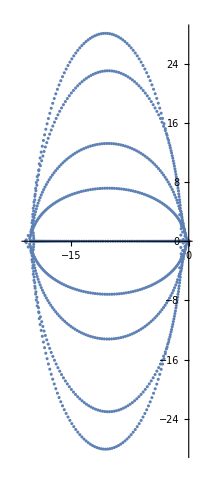

```mathematica
ComplexListPlot[eigenvaluesStabilityMatrixNonZeroPaddedModel]
```

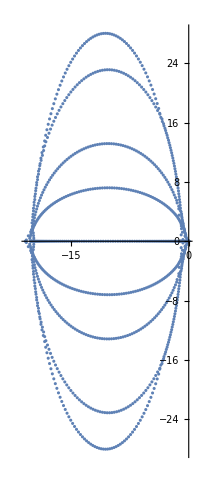

```mathematica
ComplexListPlot[eigenvaluesStabilityMatrixZeroPaddedModel]
```

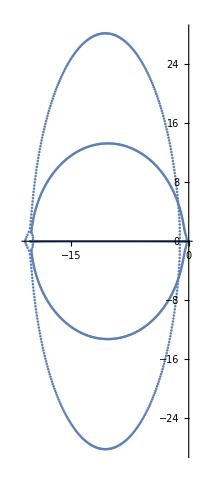

```mathematica
ComplexListPlot[eigenvaluesStabilityMatrixReference]
```